```mathematica
LaunchKernels[]
(*Needs["FourierSeries`"]*)
```

{KernelObject(1,local),KernelObject(2,local)}

```mathematica
(*константы*)
α=1/137;lc=SetPrecision[3.86 10^-11,MachinePrecision];cc=SetPrecision[3 10^(10),MachinePrecision];mee=SetPrecision[0.511 10^6,MachinePrecision];
(*параметры траектории*)
γ=SetPrecision[500,MachinePrecision];(*гамма-фактор заряженных частиц*)
λo=SetPrecision[40/25 10^(-3)/lc,MachinePrecision];(*период ондулятора 1 см*)
kdip=SetPrecision[0,MachinePrecision];(*параметр дипольности*)
βp=Sqrt[1-(1+kdip^2)/γ^2];(*составляющая скорости вдоль оси 3*)
ω=(2 π)/λo βp;(*круговая частота колебаний в частиц однуляторе*)
(*χt=1;(*χt -- киральность спирали траектории; γ=235, K=1.29,lambda_0=3.3cm -- SLAC, Hemsing*)*)
θi=0;(*угол падения частицы относительно нормали к поверхности*)
No=2;(*число периодов ондулятора*)
Lt=No 2 Pi/ω;(*время пролета ондулятора*)
mMax =10; (*ожидаемое максимальное значение m*)
Print["Магнитное поле в ондуляторе H (Гс): ",(2 Pi Sqrt[2]kdip/λo) 4.41 10^(13)]
```

Магнитное поле в ондуляторе H (Гс): 0.

```mathematica
Lz= βp Lt;(*толщина пластины холестерика*)
Nc=40;(*число периодов холестерика*)
qc=Pi Nc/Lz;(*волновой вектор холестерика*)
(*диэлектрическая проницаемость*)
(*ϵc[ω1_?NumberQ]:=SetPrecision[Module[{λ=2 Pi/ω1 lc 10^4},
If[λ≥0.275&&λ≤0.546,(1+0.014755297/(426.29740-λ^(-2)))^2,1]],90](*гелий*)*)
ϵpp[k0_]=SetPrecision[2.22,MachinePrecision];(*перпендикулярная диэлектрическая проницаемость*)
ϵpl[k0_]=SetPrecision[2.49,MachinePrecision];(*параллельная диэлектрическая проницаемость*)
dec[k0_]=(ϵpl[k0]-ϵpp[k0])/ϵpp[k0];(*анизотропия*)
Print["Волновой вектор холестерика в эВ: ",qc mee]
Print["Толщина пластины холестерика в мкм: ",Lz lc 10^4]
Module[{xx=3.5/mee,npp=6/7,kkp,k3bb,epp,dde},(*предполагаемая энергия фотона и n_perp*)
epp=ϵpp[xx];
dde=dec[xx];
kkp=xx npp;
k3bb=Sqrt[epp xx^2-kkp^2];
Print["Анизотропия de: ",dde];
Print["Параметры малости ТВ по de: ", Abs[(dde/4) ϵpp[xx]/(ϵpp[xx]-npp^2)],", ",Abs[dde k3bb^5/(4 qc kkp^2 (k3bb^2-qc^2))]]]
```

Волновой вектор холестерика в эВ: 0.774583

Толщина пластины холестерика в мкм: 32.

Анизотропия de: 0.121622

Параметры малости ТВ по de: 0.0454452, 0.35005

```mathematica
e3={0,0,1};
e1={1,0,0};
e2={0,1,0};
ep=e1+ⅈ e2;
em=e1-ⅈ e2;
```

```mathematica
(*xoa=kdip/(Sqrt[2] ω γ);yoa=xoa;(*амплитуды колебаний*)*)
zo=-Lz;(*начальная координата в компотоновский длинах волн. частица вылетает из пластины в сторону детектора*)
(*xo=0;yo=0;zo=0;начальные координаты в компотоновский длинах волн*)
(*ωs=χt ω;(*частота со знаком*)*)
vx0=Sin[θi] Sqrt[1-1/γ^2];vy0=0;vz0=Cos[θi] Sqrt[1-1/γ^2];(*скорость влета*)
rt[t_]={0,0,zo+βp t};
v[t_]={0,0,βp};
xo=rt[0][[1]];yo=rt[0][[2]];
```

```mathematica
tfin=Lt;
```

```mathematica
rf=rt[tfin];
vxf=0;vyf=0;vzf=Sqrt[1-1/γ^2];(*вылетает вдоль оси -- нормали к пластине*)
```

```mathematica
xp[t_]=rt[t].ep;
xm[t_]=rt[t].em;
x3[t_]=rt[t].e3;
x0[t_]=t;  (*c=1*)
vp[t_]=v[t].ep;
vm[t_]=v[t].em;
v3[t_]=v[t].e3;
```

```mathematica
k31[k0s_,kp_,de_]=√(k0s-kp^2)+1/4 de √(k0s-kp^2)+(de^2 (√(k0s-kp^2) (-(4 k0s)+3 kp^2+2)))/(64 (k0s-kp^2-1));(*правая быстрая ветвь при q=1*)
k32[k0s_,kp_,de_]=√(k0s-kp^2)+(de k0s)/(4 √(k0s-kp^2))+(de^2 (-(k0s (4 k0s^2-k0s (5 kp^2+2)+kp^4))))/(64 (k0s-kp^2-1) (k0s-kp^2)^(3/2));(*правая медленная ветвь при q=1*)
```

```mathematica
Clear[CoeffLinCombL]
```

```mathematica
CoeffLinComb[s_/;(s^2==1),k00_?NumberQ,k0_?NumberQ,k0s_?NumberQ,kp_?NumberQ,ϕ_?NumberQ,n3_?NumberQ,k3b_?NumberQ,de_?NumberQ,pf_?NumberQ,ps_?NumberQ]:=Module[{xps0,xmsm2,xps2,xms0,xpsm2,xmsm4,yps0,ymsm2,yps2,yms0,ypsm2,ymsm4,xms2,xpsm4,yms2,ypsm4,tf,ts,r,apfs,amfs,apss,amss,amfcs,apfcs,amscs,apscs,rapfs,ramfs,rapss,ramss,ramfcs,rapfcs,ramscs,rapscs,n3i,um,h0i,t0l,tfl,tsl,tpi,tm,gv,ach,al,norm},

n3i=1/n3;

xps0=1;yps0=1;
If[k0s<kp^2,xms0=0;xps2=0;xms2=0;xpsm2=0;xmsm2=0;yms0=0;yps2=0;yms2=0;ypsm2=0;ymsm2=0,
xms0=1+(de (k0s √(k0s-kp^2) (2 k0s-kp^2)))/(8 kp^2 (-k0s+kp^2+1));
xps2=(2 k0s-kp^2)/(16 (√(k0s-kp^2)+1));
xms2=-kp^2/(16 (√(k0s-kp^2)+1));
xpsm2=kp^2/(16 (√(k0s-kp^2)-1));
xmsm2=-(2 k0s-kp^2)/(16 (√(k0s-kp^2)-1));

(*медленная волна*)
yms0=-1+(de (√(k0s-kp^2) (2 k0s^2-3 k0s kp^2+kp^4)))/(8 kp^2 (-k0s+kp^2+1));
yps2=-(2 k0s-kp^2)/(16 (√(k0s-kp^2)+1));
yms2=kp^2/(16 (√(k0s-kp^2)+1));
ypsm2=kp^2/(16 (√(k0s-kp^2)-1));
ymsm2=-(2 k0s-kp^2)/(16 (√(k0s-kp^2)-1))];(*коэффициенты должны быть вещественными*)

(*xms2=0;xpsm4=0;yms2=0;ypsm4=0;(*зануляем высшие поправки*)*)

tf=Exp[-I pf ϕ]; ts=Exp[-I ps ϕ]; r=Exp[-2 I ϕ];(*фазовые множители*)
t0l=Exp[-I k00 n3 Lz];tfl=Exp[-I pf qc Lz];tsl=Exp[-I ps qc Lz];

apfs=tf (xps0+de xps2 r+de xpsm2/r);(*a_pm при z=0*)
amfs=tf(xms0+de xms2 r+de xmsm2/r);
apss=ts(yps0+de yps2 r+de ypsm2/r);
amss=ts (yms0+de yms2 r+de ymsm2/r);
amfcs=1/tf (xps0+de xps2/r+de xpsm2 r);(*a_pm сопряженное при z=0*)
apfcs=1/tf (xms0+de xms2/r+de xmsm2 r);
amscs=1/ts (yps0 +de yps2/r+de ypsm2 r);
apscs=1/ts(yms0+de yms2/r+de ymsm2 r);
(*-I K dz U11 при z=0*)
rapfs=tf (pf (xps0+kp^2/(2 k3b^2) (xps0+xms0))+(pf+2) de r (xps2+kp^2/(2 k3b^2) (xps2+xms2))+(pf-2) de/r (xpsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2)));
ramfs=tf (pf (xms0+kp^2/(2 k3b^2) (xps0+xms0))+(pf+2) de r (xms2+kp^2/(2 k3b^2) (xps2+xms2))+(pf-2) de/r (xmsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2)));
rapss=ts (ps (yps0+kp^2/(2 k3b^2) (yps0+yms0))+(ps+2) de r (yps2+kp^2/(2 k3b^2) (yps2+yms2))+(ps-2) de/r (ypsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2)));
ramss=ts (ps (yms0+kp^2/(2 k3b^2) (yps0+yms0))+(ps+2) de r (yms2+kp^2/(2 k3b^2) (yps2+yms2))+(ps-2) de/r (ymsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2)));
(*U21*)
ramfcs=-1/tf (pf (xps0+kp^2/(2 k3b^2) (xps0+xms0))+(pf+2) de/r (xps2+kp^2/(2 k3b^2) (xps2+xms2))+(pf-2) de r (xpsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2)));
rapfcs=-1/tf (pf (xms0+kp^2/(2 k3b^2) (xps0+xms0))+(pf+2) de/r (xms2+kp^2/(2 k3b^2) (xps2+xms2))+(pf-2) de r (xmsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2)));
ramscs=-1/ts (ps (yps0+kp^2/(2 k3b^2) (yps0+yms0))+(ps+2) de/r (yps2+kp^2/(2 k3b^2) (yps2+yms2))+(ps-2) de r (ypsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2)));
rapscs=-1/ts (ps (yms0+kp^2/(2 k3b^2) (yps0+yms0))+(ps+2) de/r (yms2+kp^2/(2 k3b^2) (yps2+yms2))+(ps-2) de r (ymsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2)));

um={{apfs,apss,apfcs,apscs},{amfs,amss,amfcs,amscs},{rapfs,rapss,rapfcs,rapscs},{ramfs,ramss,ramfcs,ramscs}};
h0i={{(n3i-1)/(4 √2),(n3i+1)/(4 √2),-(n3i-1)/(4 √2 k0),(n3i+1)/(4 √2 k0)},{(n3i+1)/(4 √2),(n3i-1)/(4 √2),(n3i+1)/(4 √2 k0),-(n3i-1)/(4 √2 k0)},{-(n3i+1)/(4 √2),-(n3i-1)/(4 √2),(n3i+1)/(4 √2 k0),-(n3i-1)/(4 √2 k0)},{-(n3i-1)/(4 √2),-(n3i+1)/(4 √2),-(n3i-1)/(4 √2 k0),(n3i+1)/(4 √2 k0)}};
(*h0={{(n3-1)/(√2),(n3+1)/(√2),(-n3-1)/(√2),(1-n3)/(√2)},{(n3+1)/(√2),(n3-1)/(√2),(1-n3)/(√2),(-n3-1)/(√2)},{(k0 (1-n3))/(√2),(k0 (n3+1))/(√2),(k0 (n3+1))/(√2),(k0 (1-n3))/(√2)},{(k0 (n3+1))/(√2),(k0 (1-n3))/(√2),(k0 (1-n3))/(√2),(k0 (n3+1))/(√2)}};*)

tpi={{1/t0l,0,0,0},{0,1/t0l,0,0},{0,0,t0l,0},{0,0,0,t0l}};
tm={{tfl,0,0,0},{0,tsl,0,0},{0,0,1/tfl,0},{0,0,0,1/tsl}};

gv={(n3-s)/(√2),(n3+s)/(√2),(k0 (1-n3 s))/(√2),(k0 (n3 s+1))/(√2)};

ach=Inverse[um].gv;
al=tpi.h0i.um.tm.ach;
norm=Sqrt[2/(1+Conjugate[al].al)];

{norm,ach,al,{xms0,xps2,xms2,xpsm2,xmsm2},{yms0,yps2,yms2,ypsm2,ymsm2}}](*выдает ответ в виде списка*)
```

```mathematica
ModeFun1[t_?NumberQ,kp_?NumberQ,ϕ_?NumberQ,xms0_?NumberQ,xps2_?NumberQ,xms2_?NumberQ,xpsm2_?NumberQ,xmsm2_?NumberQ,de_?NumberQ,pf_?NumberQ,k3b_?NumberQ,rf1_?NumberQ]:=Module[{xps0,tf,r,apfs,amfs,a3fs,amfcs,apfcs,a3fcs},
xps0=1;
(*xms2=0;xpsm4=0;(*зануляем высшие поправки*)*)

tf=Exp[I pf (qc x3[t]-ϕ)];r=rf1;(*фазовые множители*)

apfs=tf (xps0+de xps2 r+de xpsm2/r);(*a_pm,3*)
amfs=tf(xms0+de xms2 r+de xmsm2/r);
a3fs=-kp/(2 k3b^2) tf ((pf xps0+de (pf+2) xps2 r+de (pf-2) xpsm2/r)+(pf xms0+de (pf+2) xms2 r+de (pf-2) xmsm2/r));
amfcs=1/tf (xps0+de xps2/r+de xpsm2 r);(*a_pm,3 сопряженное*)
apfcs=1/tf(xms0+de xms2/r+de xmsm2 r);
a3fcs=kp/(2 k3b^2)/tf ((pf xps0+de (pf+2) xps2/r+de (pf-2) xpsm2 r)+(pf xms0+de (pf+2) xms2/r+de (pf-2) xmsm2 r));

{{apfs Exp[I ϕ],amfs Exp[-I ϕ],a3fs},{apfcs Exp[I ϕ],amfcs Exp[-I ϕ],a3fcs}}](*ответ в виде списка без общего фазового множителя*)
```

```mathematica
ModeFun2[t_?NumberQ,kp_?NumberQ,ϕ_?NumberQ,yms0_?NumberQ,yps2_?NumberQ,yms2_?NumberQ,ypsm2_?NumberQ,ymsm2_?NumberQ,de_?NumberQ,ps_?NumberQ,k3b_?NumberQ,rf1_?NumberQ]:=Module[{yps0,ts,r,apss,amss,a3ss,amscs,apscs,a3scs},
yps0=1;
(*yms2=0;ypsm4=0;(*зануляем высшие поправки*)*)

ts=Exp[I ps (qc x3[t]-ϕ)];r=rf1;(*фазовые множители*)

apss=ts (yps0+de yps2 r+de ypsm2/r);(*a_pm,3*)
amss=ts(yms0+de yms2 r+de ymsm2/r);
a3ss=-kp/(2 k3b^2) ts ((ps yps0+de (ps+2) yps2 r+de (ps-2) ypsm2/r)+(ps yms0+de (ps+2) yms2 r+de (ps-2) ymsm2/r));
amscs=1/ts (yps0+de yps2/r+de ypsm2 r);(*a_pm,3 сопряженное*)
apscs=1/ts(yms0+de yms2/r+de ymsm2 r);
a3scs=kp/(2 k3b^2)/ts ((ps yps0+de (ps+2) yps2/r+de (ps-2) ypsm2 r)+(ps yms0+de (ps+2) yms2/r+de (ps-2) ymsm2 r));

{{apss Exp[I ϕ],amss Exp[-I ϕ],a3ss},{apscs Exp[I ϕ],amscs Exp[-I ϕ],a3scs}} ](*ответ в виде списка без общего фазового множителя*)
```

```mathematica
Clear[InteGrand]
```

```mathematica
InteGrand[t_?NumberQ,k00_?NumberQ,kpl_,kp_?NumberQ,ϕ_?NumberQ,achli_,xxsl_,yysl_,de_?NumberQ,pf_?NumberQ,ps_?NumberQ,k3b_?NumberQ]:=Module[{rfff,afrl,asrl,vpt,vmt,v3t},
rfff=Exp[2 I (qc x3[t]-ϕ)];(*фазовый множитель*)

afrl=ModeFun1[t,kp,ϕ,xxsl[[1]],xxsl[[2]],xxsl[[3]],xxsl[[4]],xxsl[[5]],de,pf,k3b,rfff];
asrl=ModeFun2[t,kp,ϕ,yysl[[1]],yysl[[2]],yysl[[3]],yysl[[4]],yysl[[5]],de,ps,k3b,rfff];

vpt=vp[t];vmt=vm[t];v3t=v3[t];

(achli[[1]] (1/2 (vpt afrl[[1,2]]+vmt afrl[[1,1]])+v3t afrl[[1,3]])+achli[[3]] (1/2 (vpt afrl[[2,2]]+vmt afrl[[2,1]])+v3t afrl[[2,3]])+achli[[2]] (1/2 (vpt asrl[[1,2]]+vmt asrl[[1,1]])+v3t asrl[[1,3]])+achli[[4]] (1/2 (vpt asrl[[2,2]]+vmt asrl[[2,1]])+v3t asrl[[2,3]])) Exp[-I k00 x0[t]+I (kpl[[1]] rt[t][[1]]+kpl[[2]] rt[t][[2]])]]
```

```mathematica
fps[ss_/;(ss^2==1),cffs_,sffs_,npss_,n3ss_]={cffs n3ss-I ss sffs,sffs n3ss+I ss cffs,-npss}/Sqrt[2];
fms[ss_/;(ss^2==1),cffs_,sffs_,npss_,n3ss_]={-cffs n3ss-I ss sffs,-sffs n3ss+I ss cffs,-npss}/Sqrt[2];
```

```mathematica
AmplitEnd[s1_/;(s1^2==1),k00_?NumberQ,kpl_,alli_,cff_?NumberQ,sff_?NumberQ,nps_?NumberQ,n3s_?NumberQ]:=Module[{contR,contL,contF},
contR=(alli[[1]] fps[1,cff,sff,nps,n3s]+alli[[2]] fps[-1,cff,sff,nps,n3s]).{vx0,vy0,vz0} I Exp[I (k00 n3s zo+kpl[[1]] xo+ kpl[[2]] yo)]/(k00 (1-n3s vz0)-kpl[[1]] vx0- kpl[[2]] vy0);
contL=(alli[[3]] fms[1,cff,sff,nps,n3s]+alli[[4]] fms[-1,cff,sff,nps,n3s]).{vx0,vy0,vz0} I Exp[I (-k00 n3s zo+kpl[[1]] xo+ kpl[[2]] yo)]/(k00 (1+n3s vz0)-kpl[[1]] vx0- kpl[[2]] vy0);(*вклад слева от пластины*)

contF=-I fps[s1,cff,sff,nps,n3s].{vxf,vyf,vzf} Exp[-I (k00 tfin-k00 n3s rf[[3]]-kpl[[1]] rf[[1]]-kpl[[2]] rf[[2]])]/(k00 (1-n3s vzf)-kpl[[1]] vxf- kpl[[2]] vyf);(*вклад справа от пластины*)

contR+contL+contF](*вклад без общего нормировочного множителя*)
```

```mathematica
AmplitPlane[s1_?NumberQ,k00_?NumberQ,npx_?NumberQ,npy_?NumberQ]:=Module[{kpl,ϕ,cff,sff,k0,k0s,np,n3,kp,k3b,de,pf,ps,coeffList,cnorm,ach,al,xxl,yyl,amplPlate,amplE},
kpl=k00 {npx,npy};
ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];(*часто используемые постоянные*)
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
np=Sqrt[npx^2+npy^2];
n3=Sqrt[1-np^2];
kp=k0 np;
k3b=Sqrt[k0s-kp^2];
de=dec[k00];
pf=k31[k0s,kp,de];(*импульсы с q=1*)
ps=k32[k0s,kp,de];

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,n3,k3b,de,pf,ps];
cnorm=coeffList[[1]];
ach=coeffList[[2]];
al=coeffList[[3]];
xxl=coeffList[[4]];
yyl=coeffList[[5]];

amplPlate=NIntegrate[InteGrand[t,k00,kpl,kp,ϕ,ach,xxl,yyl,de,pf,ps,k3b],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0},MaxRecursion->12,MinRecursion->5];(*основной интеграл*)

amplE=AmplitEnd[s1,k00,kpl,al,cff,sff,np,n3];(*концы*)

cnorm (amplPlate+amplE)](*полная амплитуда без постоянного общего множителя*)
```

```mathematica
Clear[dProbabPlane]
```

```mathematica
dProbabPlane[s1_/;(s1^2==1),k001_?NumberQ,npx1_?NumberQ,npy1_?NumberQ]:=Module[{npx,npy,k00,kpl,ϕ,cff,sff,k0,k0s,np,n3,kp,k3b,de,pf,ps,coeffList,cnorm,ach,al,xxl,yyl,amplPlate,amplE},
npx=SetPrecision[npx1,MachinePrecision];
npy=SetPrecision[npy1,MachinePrecision];
k00=SetPrecision[k001,MachinePrecision];

kpl=k00 {npx,npy};
ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];(*часто используемые постоянные*)
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
np=Sqrt[npx^2+npy^2];
n3=Sqrt[1-np^2];
kp=k0 np;
k3b=Sqrt[k0s-kp^2];
de=dec[k00];
pf=k31[k0s,kp,de];(*импульсы с q=1*)
ps=k32[k0s,kp,de];

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,n3,k3b,de,pf,ps];
cnorm=coeffList[[1]];
ach=coeffList[[2]];
al=coeffList[[3]];
xxl=coeffList[[4]];
yyl=coeffList[[5]];

amplPlate=NIntegrate[InteGrand[t,k00,kpl,kp,ϕ,ach,xxl,yyl,de,pf,ps,k3b],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0},MaxRecursion->12,MinRecursion->5];(*основной интеграл. возможно, лучше передавать в процедуры t как число*)

amplE=AmplitEnd[s1,k00,kpl,al,cff,sff,np,n3];(*концы*)

α/(4 Pi^2)k00 Abs[cnorm(amplPlate+amplE)]^2](*вероятность в единицу телесного угла на единичный интервал энергии*)
```

```mathematica
(*------------конец плосковолнового кода----------------------------------*)
```

```mathematica
(*------------закрученные фотоны------------------------------------------*)
```

```mathematica
Clear[AmplTwistTab]
```

```mathematica
AmplTwistTab[s_/;(s^2==1),k00_?NumberQ,kpp_?NumberQ]:=Module[{Npt,np,amplPlTab,amplTwTab},
np=kpp/k00;
Npt=2^(Floor[Log[2,20 mMax]]);(*число элементов таблицы*)

amplPlTab=ParallelTable[AmplitPlane[s,k00,np Cos[N[2 Pi (n1-1)/Npt]],np Sin[N[2 Pi (n1-1)/Npt]]],{n1,1,Npt}];(*таблица значений плосковолновой амплитуды*)
amplTwTab=-np^(1/2)/2 Chop[Fourier[amplPlTab,FourierParameters->{-1,1}]];(*таблица значений закрученной амплитуды с m=s-1 и m+Npt=m*)

{Npt,amplPlTab,amplTwTab}](*на выходе: {число элементов, табл1, табл2}*)
```

```mathematica
AmplTwist[mm_?IntegerQ,amplli_]:=Module[{Npt=Length[amplli]},
I^(-mm)amplli[[1+Mod[mm,Npt]]]](*амплитуда с правильной фазой*)
```

```mathematica
dProbabTwist[mm_?IntegerQ,amplli_]:=2 α/Pi Abs[AmplTwist[mm,amplli]]^2
```

```mathematica
(*нужно сначала вызвать ll=AmplTwistTab[s,k00,kpp], а потом dProbabTwist[m,ll[[3]]] для нужного значения m*)
```

```mathematica
(*------------конец кода для закрученных фотонов-------------------------------*)
```

```mathematica
spectpp[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=2 γ^2 qc (2nn+1)/(1+γ^2 npp^2-γ^2 (ϵpp[k0]-1));(*при npp=χ энергия резко возрастает до вакуумной*)
spectpl[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=2 γ^2 qc (2nn+1)/(1+γ^2 npp^2-γ^2 (ϵpl[k0]-1));
spect3pp[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=-qc (2nn+1)/(1+ϵpp[k0]^(1/2));
spect3pl[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=-qc (2nn+1)/(1+ϵpl[k0]^(1/2));
```

```mathematica
EqnSpecX[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00-b3 qc (2 nn +k31[k0s,kp,de])]
EqnSpecTX[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00+b3 qc (2 nn +k31[k0s,kp,de])]
EqnSpecY[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00-b3 qc (2 nn +k32[k0s,kp,de])]
EqnSpecTY[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00+b3 qc (2 nn +k32[k0s,kp,de])]
```

```mathematica
(*-------примеры-------*)
```

```mathematica
dProbabPlane[1,1.5/mee,1/γ,1/γ]//Timing(*машинная точность. больше интераций в интеграле*)
dProbabPlane[1,1.6/mee,1/γ,1/γ]//Timing
dProbabPlane[1,1.4/mee,1/γ,1/γ]//Timing
```

{2.62082,5.699×10^6}

{3.55682,190114.}

{2.07481,1.99965×10^6}

```mathematica
dProbabPlane[1,1.5/mee,1/γ,1/γ]//Timing(*машинная точность. больше интераций в интеграле*)
dProbabPlane[1,1.6/mee,1/γ,1/γ]//Timing
dProbabPlane[1,1.4/mee,1/γ,1/γ]//Timing
```

{2.57402,5.699×10^6}

{3.58802,190114.}

{2.04361,1.99965×10^6}

```mathematica
dProbabPlane[1,1.5/mee,1/γ,1/γ]//Timing(*машинная точность. больше интераций в интеграле*)
dProbabPlane[1,1.6/mee,1/γ,1/γ]//Timing
dProbabPlane[1,1.4/mee,1/γ,1/γ]//Timing
```

{2.60522,1.26259×10^6}

{3.63482,42890.}

{2.02801,440632.}

```mathematica
dProbabPlane[1,1.5/mee,1/γ,1/γ]//Timing(*машинная точность*)
dProbabPlane[1,1.6/mee,1/γ,1/γ]//Timing
dProbabPlane[1,1.4/mee,1/γ,1/γ]//Timing
```

{1.17001,1.83484×10^6}

{1.18561,3.87669×10^6}

{1.59121,86936.4}

```mathematica
dProbabPlane[1,1.5/mee,1/γ,1/γ]//Timing(*точность 90*)
dProbabPlane[1,1.6/mee,1/γ,1/γ]//Timing
dProbabPlane[1,1.4/mee,1/γ,1/γ]//Timing
```

{1.56001,1.83484×10^6}

{1.59121,3.87669×10^6}

{2.12161,86936.4}

```mathematica
2^(Floor[Log[2,20 mMax]])
```

128

```mathematica
llts1=AmplTwistTab[1,1.5/mee,1.5/mee/γ];
lltsm1=AmplTwistTab[-1,1.5/mee,1.5/mee/γ];
```

```mathematica
tms1=Table[{m,dProbabTwist[m,llts1[[3]]]},{m,-mMax,mMax}];
tmsm1=Table[{m,dProbabTwist[m,lltsm1[[3]]]},{m,-mMax,mMax}];
```

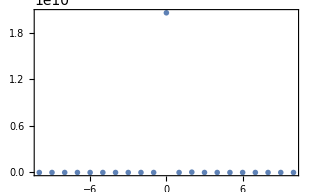
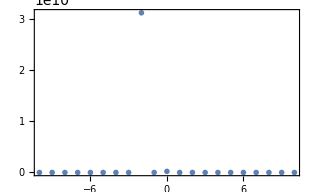

```mathematica
{ListPlot[tms1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tmsm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*спектр*)
```

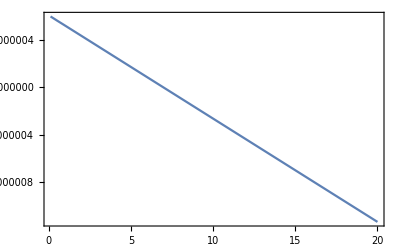
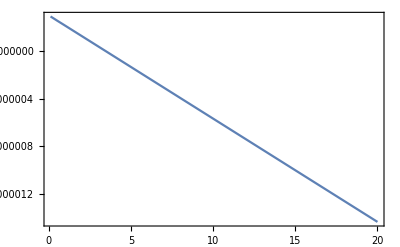
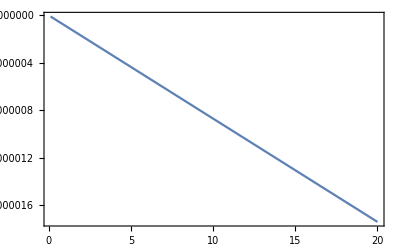
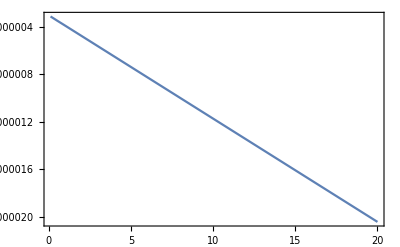

```mathematica
{Plot[EqnSpecX[xx/mee,1/2,-2],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/2,-1],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/2,0],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/2,1],{xx,1/10,20},Frame->True,PlotRange->Full]}
```

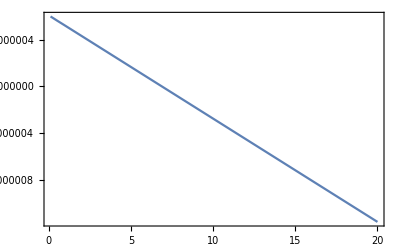
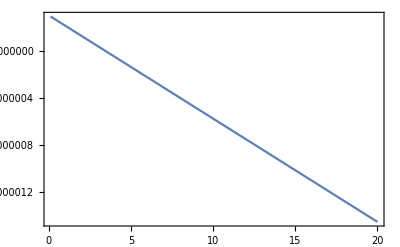
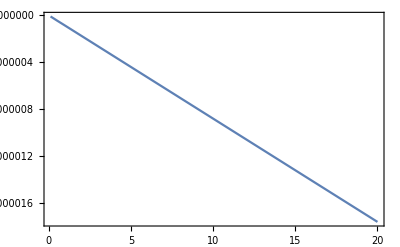
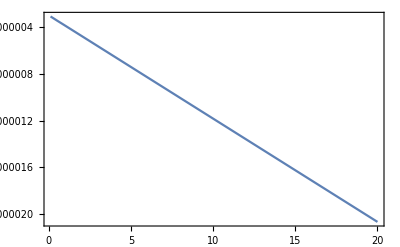

```mathematica
{Plot[EqnSpecY[xx/mee,1/2,-2],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/2,-1],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/2,0],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/2,1],{xx,1/10,20},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecY[xx/mee,1/2,-2],{xx,5}]
FindRoot[EqnSpecY[xx/mee,1/2,-1],{xx,5}]
FindRoot[EqnSpecX[xx/mee,1/2,-2],{xx,5}]
FindRoot[EqnSpecX[xx/mee,1/2,-1],{xx,5}]
```

{xx→6.88442}

{xx→3.44233}

{xx→6.96415}

{xx→3.48218}

```mathematica
tk01s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/2,0]},{x,3,4,0.005}]
```

(3. | 97.8162
3.005 | 47.3641
3.01 | 23.9116
3.015 | 9.40647
3.02 | 24.9841
3.025 | 73.2429
3.03 | 97.7374
3.035 | 191.394
3.04 | 244.884
3.045 | 257.341
3.05 | 388.853
3.055 | 323.179
3.06 | 337.694
3.065 | 366.422
3.07 | 243.8
3.075 | 242.835
3.08 | 162.571
3.085 | 91.3108
3.09 | 61.0798
3.095 | 18.0185
3.1 | 9.72072
3.105 | 25.2343
3.11 | 43.8838
3.115 | 107.982
3.12 | 165.377
3.125 | 186.223
3.13 | 317.046
3.135 | 286.139
3.14 | 311.237
3.145 | 382.449
3.15 | 267.151
3.155 | 287.968
3.16 | 226.664
3.165 | 139.409
3.17 | 118.838
3.175 | 50.4362
3.18 | 21.7558
3.185 | 10.1927
3.19 | 13.1283
3.195 | 46.1651
3.2 | 91.4693
3.205 | 115.888
3.21 | 227.033
3.215 | 226.465
3.22 | 257.9
3.225 | 357.653
3.23 | 262.275
3.235 | 301.256
3.24 | 272.18
3.245 | 177.513
3.25 | 178.699
3.255 | 96.2748
3.26 | 52.7064
3.265 | 28.2678
3.27 | 8.22945
3.275 | 14.2111
3.28 | 36.5576
3.285 | 56.9027
3.29 | 133.618
3.295 | 150.912
3.3 | 182.12
3.305 | 284.769
3.31 | 219.507
3.315 | 265.338
3.32 | 270.778
3.325 | 183.285
3.33 | 207.115
3.335 | 131.472
3.34 | 83.1841
3.345 | 65.3456
3.35 | 25.2999
3.355 | 14.913
3.36 | 14.2329
3.365 | 20.4478
3.37 | 53.1153
3.375 | 64.8636
3.38 | 80.189
3.385 | 133.032
3.39 | 99.1104
3.395 | 112.997
3.4 | 113.344
3.405 | 64.6466
3.41 | 61.6922
3.415 | 34.251
3.42 | 21.0055
3.425 | 34.6037
3.43 | 49.9416
3.435 | 111.422
3.44 | 206.039
3.445 | 234.4
3.45 | 454.227
3.455 | 496.417
3.46 | 544.369
3.465 | 881.3
3.47 | 685.308
3.475 | 823.96
3.48 | 960.362
3.485 | 660.264
3.49 | 834.121
3.495 | 632.667
3.5 | 441.613
3.505 | 480.863
3.51 | 237.708
3.515 | 159.942
3.52 | 106.193
3.525 | 35.1398
3.53 | 38.636
3.535 | 56.2228
3.54 | 91.0866
3.545 | 222.021
3.55 | 224.298
3.555 | 323.904
3.56 | 473.227
3.565 | 363.238
3.57 | 516.528
3.575 | 460.436
3.58 | 341.989
3.585 | 425.923
3.59 | 240.006
3.595 | 174.008
3.6 | 135.803
3.605 | 42.7034
3.61 | 15.4819
3.615 | 4.54311
3.62 | 17.9299
3.625 | 80.8866
3.63 | 108.767
3.635 | 186.816
3.64 | 325.369
3.645 | 271.496
3.65 | 420.42
3.655 | 426.135
3.66 | 331.891
3.665 | 462.035
3.67 | 293.453
3.675 | 234.291
3.68 | 228.411
3.685 | 94.7316
3.69 | 59.0906
3.695 | 20.4173
3.7 | 1.37277
3.705 | 17.1274
3.71 | 40.6804
3.715 | 95.074
3.72 | 205.589
3.725 | 191.613
3.73 | 325.725
3.735 | 376.174
3.74 | 307.001
3.745 | 469.928
3.75 | 332.135
3.755 | 282.693
3.76 | 324.066
3.765 | 157.165
3.77 | 126.593
3.775 | 74.5897
3.78 | 17.4727
3.785 | 4.29566
3.79 | 6.10607
3.795 | 34.0233
3.8 | 105.322
3.805 | 117.487
3.81 | 227.314
3.815 | 303.57
3.82 | 262.494
3.825 | 439.388
3.83 | 345.147
3.835 | 308.453
3.84 | 402.716
3.845 | 217.752
3.85 | 200.847
3.855 | 155.377
3.86 | 57.6887
3.865 | 35.1341
3.87 | 5.9698
3.875 | 4.5166
3.88 | 35.1434
3.885 | 55.9153
3.89 | 135.35
3.895 | 216.014
3.9 | 202.973
3.905 | 373.574
3.91 | 328.128
3.915 | 306.763
3.92 | 448.335
3.925 | 265.417
3.93 | 266.323
3.935 | 247.998
3.94 | 112.441
3.945 | 98.6575
3.95 | 39.3917
3.955 | 6.29076
3.96 | 5.29603
3.965 | 15.2748
3.97 | 61.9627
3.975 | 127.675
3.98 | 137.276
3.985 | 284.047
3.99 | 282.697
3.995 | 278.193
4. | 451.392)

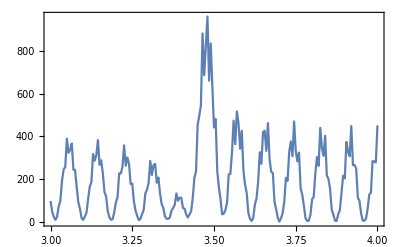

```mathematica
ListLinePlot[tk01s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk01sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/2,0]},{x,3,4,0.005}]
```

(3. | 160.211
3.005 | 127.179
3.01 | 117.038
3.015 | 79.4877
3.02 | 68.0089
3.025 | 53.9282
3.03 | 40.0973
3.035 | 57.7922
3.04 | 62.3117
3.045 | 67.6425
3.05 | 115.813
3.055 | 113.907
3.06 | 128.814
3.065 | 170.988
3.07 | 143.549
3.075 | 158.589
3.08 | 153.924
3.085 | 122.802
3.09 | 120.352
3.095 | 89.5771
3.1 | 74.7415
3.105 | 60.729
3.11 | 44.4392
3.115 | 53.2726
3.12 | 50.713
3.125 | 53.5438
3.13 | 90.1924
3.135 | 88.174
3.14 | 101.958
3.145 | 143.286
3.15 | 121.499
3.155 | 138.884
3.16 | 145.377
3.165 | 116.26
3.17 | 121.048
3.175 | 97.3556
3.18 | 79.8655
3.185 | 68.9971
3.19 | 51.2098
3.195 | 52.7779
3.2 | 45.653
3.205 | 45.9053
3.21 | 71.4802
3.215 | 68.3217
3.22 | 80.9542
3.225 | 117.937
3.23 | 101.258
3.235 | 120.526
3.24 | 134.918
3.245 | 109.2
3.25 | 121.539
3.255 | 105.389
3.26 | 87.0028
3.265 | 82.4262
3.27 | 63.4241
3.275 | 59.4966
3.28 | 49.6473
3.285 | 45.5607
3.29 | 59.5831
3.295 | 53.0024
3.3 | 62.2851
3.305 | 89.8514
3.31 | 77.5206
3.315 | 96.4868
3.32 | 115.497
3.325 | 96.8569
3.33 | 117.56
3.335 | 112.936
3.34 | 99.431
3.345 | 108.569
3.35 | 91.9368
3.355 | 88.797
3.36 | 81.1528
3.365 | 69.0944
3.37 | 71.7157
3.375 | 53.5728
3.38 | 49.8764
3.385 | 52.4249
3.39 | 35.2592
3.395 | 39.3294
3.4 | 47.5725
3.405 | 43.8341
3.41 | 67.9174
3.415 | 94.7778
3.42 | 119.87
3.425 | 188.549
3.43 | 226.166
3.435 | 309.49
3.44 | 404.865
3.445 | 437.651
3.45 | 599.032
3.455 | 626.807
3.46 | 674.716
3.465 | 847.355
3.47 | 745.229
3.475 | 832.744
3.48 | 873.406
3.485 | 709.928
3.49 | 798.125
3.495 | 664.942
3.5 | 542.095
3.505 | 560.296
3.51 | 379.58
3.515 | 322.893
3.52 | 279.546
3.525 | 172.685
3.53 | 165.466
3.535 | 129.387
3.54 | 105.463
3.545 | 136.837
3.55 | 120.074
3.555 | 143.485
3.56 | 178.251
3.565 | 152.016
3.57 | 188.428
3.575 | 175.831
3.58 | 141.373
3.585 | 154.482
3.59 | 104.638
3.595 | 77.8668
3.6 | 63.9948
3.605 | 29.8149
3.61 | 21.9438
3.615 | 17.0607
3.62 | 19.0398
3.625 | 42.9199
3.63 | 53.0315
3.635 | 83.0477
3.64 | 123.159
3.645 | 118.955
3.65 | 161.412
3.655 | 166.265
3.66 | 143.032
3.665 | 167.091
3.67 | 124.7
3.675 | 98.7512
3.68 | 88.121
3.685 | 45.5494
3.69 | 28.8631
3.695 | 15.261
3.7 | 6.00644
3.705 | 14.3702
3.71 | 22.4374
3.715 | 45.503
3.72 | 80.2203
3.725 | 87.8307
3.73 | 131.292
3.735 | 149.423
3.74 | 138.949
3.745 | 174.614
3.75 | 143.727
3.755 | 123.86
3.76 | 122.682
3.765 | 74.2988
3.77 | 55.2795
3.775 | 35.3821
3.78 | 12.4788
3.785 | 8.64834
3.79 | 7.91045
3.795 | 19.9438
3.8 | 44.6551
3.805 | 57.1165
3.81 | 96.685
3.815 | 122.804
3.82 | 124.345
3.825 | 168.291
3.83 | 152.02
3.835 | 141.308
3.84 | 152.96
3.845 | 104.759
3.85 | 88.5639
3.855 | 67.6508
3.86 | 32.4846
3.865 | 21.0708
3.87 | 8.96435
3.875 | 7.75351
3.88 | 20.3359
3.885 | 30.7452
3.89 | 62.0531
3.895 | 89.9449
3.9 | 100.625
3.905 | 147.934
3.91 | 146.735
3.915 | 146.556
3.92 | 171.71
3.925 | 130.187
3.93 | 120.849
3.935 | 104.944
3.94 | 61.4213
3.945 | 47.7637
3.95 | 25.2263
3.955 | 10.3842
3.96 | 11.36
3.965 | 13.656
3.97 | 33.3966
3.975 | 57.0146
3.98 | 72.0094
3.985 | 117.179
3.99 | 128.422
3.995 | 138.223
4. | 174.809)

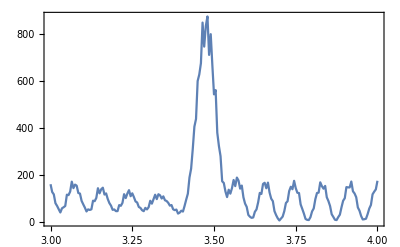

```mathematica
ListLinePlot[tk01sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
ll2ts1=AmplTwistTab[1,3.48/mee,3.48/mee/2];
ll2tsm1=AmplTwistTab[-1,3.48/mee,3.48/mee/2];
```

```mathematica
tm2s1=Table[{m,dProbabTwist[m,ll2ts1[[3]]]},{m,-mMax,mMax}];
tm2sm1=Table[{m,dProbabTwist[m,ll2tsm1[[3]]]},{m,-mMax,mMax}];
```

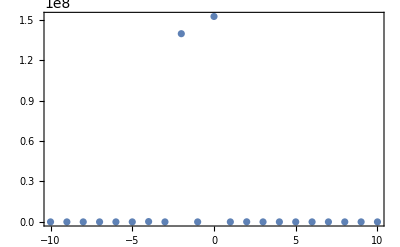
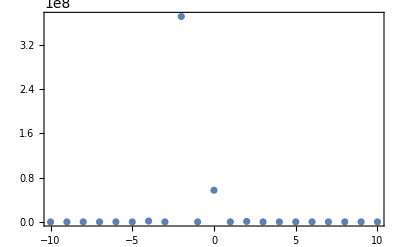

```mathematica
{ListPlot[tm2s1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tm2sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*np=6/7*)
```

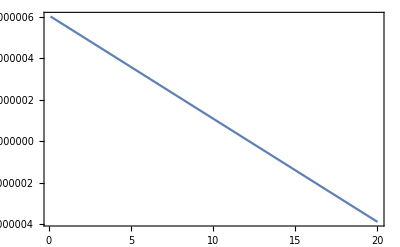
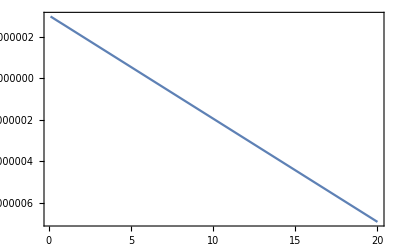
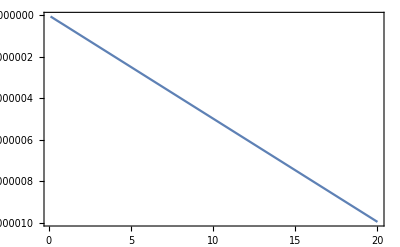
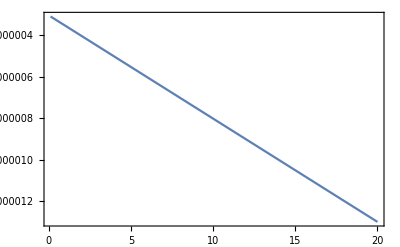

```mathematica
{Plot[EqnSpecX[xx/mee,6/7,-2],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,6/7,-1],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,6/7,0],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,6/7,1],{xx,1/10,20},Frame->True,PlotRange->Full]}
```

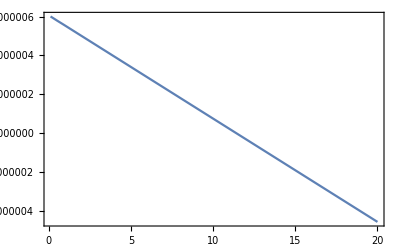
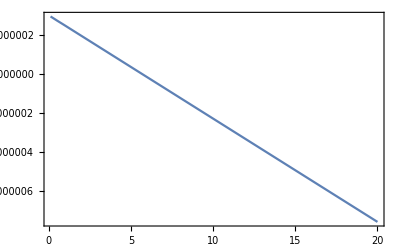
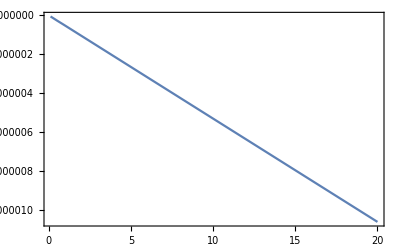
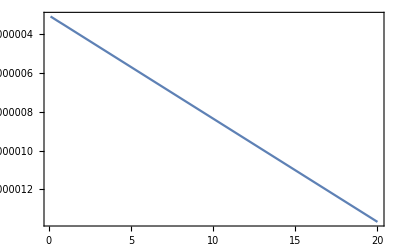

```mathematica
{Plot[EqnSpecY[xx/mee,6/7,-2],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,6/7,-1],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,6/7,0],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,6/7,1],{xx,1/10,20},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecY[xx/mee,6/7,-2],{xx,5}]
FindRoot[EqnSpecY[xx/mee,6/7,-1],{xx,5}]
FindRoot[EqnSpecX[xx/mee,6/7,-2],{xx,5}]
FindRoot[EqnSpecX[xx/mee,6/7,-1],{xx,5}]
```

{xx→11.3992}

{xx→5.69981}

{xx→12.1734}

{xx→6.08682}

```mathematica
tk02s1=ParallelTable[{x,dProbabPlane[1,x/mee,6/7,0]},{x,5.4,6.5,0.005}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

(5.4 | 51.7823
5.405 | 60.1607
5.41 | 57.9764
5.415 | 50.273
5.42 | 52.8156
5.425 | 48.8398
5.43 | 40.9219
5.435 | 38.8692
5.44 | 34.2258
5.445 | 27.8301
5.45 | 24.0001
5.455 | 20.7605
5.46 | 17.1532
5.465 | 14.6667
5.47 | 14.9206
5.475 | 14.4935
5.48 | 15.4358
5.485 | 20.0302
5.49 | 22.0343
5.495 | 26.5739
5.5 | 34.2871
5.505 | 36.8974
5.51 | 43.2417
5.515 | 51.0986
5.52 | 52.0679
5.525 | 57.4324
5.53 | 62.3812
5.535 | 60.3744
5.54 | 62.9026
5.545 | 64.3947
5.55 | 60.6643
5.555 | 61.9376
5.56 | 64.4287
5.565 | 63.9676
5.57 | 71.4087
5.575 | 85.6869
5.58 | 96.7258
5.585 | 124.893
5.59 | 167.503
5.595 | 198.526
5.6 | 268.213
5.605 | 358.898
5.61 | 413.317
5.615 | 547.696
5.62 | 705.434
5.625 | 775.401
5.63 | 993.327
5.635 | 1231.89
5.64 | 1293.84
5.645 | 1601.64
5.65 | 1925.65
5.655 | 1940.35
5.66 | 2324.68
5.665 | 2726.85
5.67 | 2645.71
5.675 | 3070.51
5.68 | 3530.62
5.685 | 3307.7
5.69 | 3717.8
5.695 | 4203.7
5.7 | 3810.49
5.705 | 4142.46
5.71 | 4613.39
5.715 | 4051.42
5.72 | 4249.62
5.725 | 4662.1
5.73 | 3968.51
5.735 | 4001.64
5.74 | 4317.5
5.745 | 3560.41
5.75 | 3432.94
5.755 | 3628.28
5.76 | 2892.24
5.765 | 2645.72
5.77 | 2718.43
5.775 | 2084.08
5.78 | 1786.64
5.785 | 1759.66
5.79 | 1283.79
5.795 | 1010.32
5.8 | 928.175
5.805 | 630.896
5.81 | 440.25
5.815 | 358.381
5.82 | 221.407
5.825 | 138.652
5.83 | 107.711
5.835 | 83.9378
5.84 | 94.3458
5.845 | 144.35
5.85 | 174.765
5.855 | 232.096
5.86 | 362.382
5.865 | 393.993
5.87 | 440.185
5.875 | 619.839
5.88 | 618.597
5.885 | 607.364
5.89 | 787.199
5.895 | 742.529
5.9 | 657.582
5.905 | 789.998
5.91 | 711.363
5.915 | 571.872
5.92 | 631.187
5.925 | 540.131
5.93 | 391.016
5.935 | 385.907
5.94 | 308.058
5.945 | 198.837
5.95 | 171.154
5.955 | 131.236
5.96 | 91.962
5.965 | 101.584
5.97 | 121.766
5.975 | 146.032
5.98 | 247.292
5.985 | 346.767
5.99 | 389.132
5.995 | 608.167
6. | 801.242
6.005 | 790.723
6.01 | 1112.98
6.015 | 1404.48
6.02 | 1269.26
6.025 | 1642.41
6.03 | 2021.9
6.035 | 1715.75
6.04 | 2066.9
6.045 | 2505.3
6.05 | 2025.56
6.055 | 2285.97
6.06 | 2738.12
6.065 | 2128.34
6.07 | 2255.93
6.075 | 2670.26
6.08 | 2006.88
6.085 | 1997.99
6.09 | 2330.59
6.095 | 1699.32
6.1 | 1586.11
6.105 | 1813.72
6.11 | 1284.8
6.115 | 1120.33
6.12 | 1246.47
6.125 | 857.915
6.13 | 695.741
6.135 | 746.971
6.14 | 500.521
6.145 | 377.263
6.15 | 391.089
6.155 | 260.337
6.16 | 187.466
6.165 | 197.35
6.17 | 142.613
6.175 | 109.354
6.18 | 133.503
6.185 | 116.606
6.19 | 100.995
6.195 | 139.498
6.2 | 133.243
6.205 | 115.317
6.21 | 155.902
6.215 | 146.602
6.22 | 117.558
6.225 | 146.073
6.23 | 130.906
6.235 | 94.7184
6.24 | 104.496
6.245 | 86.9696
6.25 | 54.8871
6.255 | 50.3916
6.26 | 36.5201
6.265 | 18.2866
6.27 | 11.8736
6.275 | 7.85153
6.28 | 4.70633
6.285 | 9.05752
6.29 | 19.7161
6.295 | 22.8806
6.3 | 43.7007
6.305 | 70.8577
6.31 | 66.0516
6.315 | 99.0568
6.32 | 139.853
6.325 | 115.121
6.33 | 148.708
6.335 | 195.118
6.34 | 147.565
6.345 | 169.394
6.35 | 210.198
6.355 | 147.948
6.36 | 151.663
6.365 | 176.921
6.37 | 115.307
6.375 | 103.754
6.38 | 109.995
6.385 | 64.0924
6.39 | 47.3998
6.395 | 40.6465
6.4 | 18.1379
6.405 | 7.84989
6.41 | 2.18632
6.415 | 0.185515
6.42 | 2.68473
6.425 | 14.3225
6.43 | 21.4833
6.435 | 34.2735
6.44 | 73.6897
6.445 | 76.099
6.45 | 88.9603
6.455 | 155.117
6.46 | 142.687
6.465 | 143.13
6.47 | 223.027
6.475 | 193.27
6.48 | 173.439
6.485 | 247.598
6.49 | 205.469
6.495 | 166.818
6.5 | 218.172)

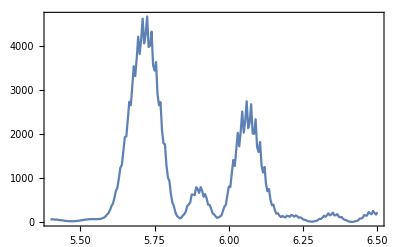

```mathematica
ListLinePlot[tk02s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk02sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,6/7,0]},{x,5.4,6.5,0.005}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

(5.4 | 649.482
5.405 | 576.001
5.41 | 631.84
5.415 | 611.068
5.42 | 510.463
5.425 | 515.832
5.43 | 464.963
5.435 | 361.018
5.44 | 329.856
5.445 | 265.441
5.45 | 183.072
5.455 | 141.754
5.46 | 88.2349
5.465 | 44.5893
5.47 | 20.4119
5.475 | 2.28782
5.48 | 0.998329
5.485 | 11.0553
5.49 | 43.6982
5.495 | 73.8991
5.5 | 118.786
5.505 | 201.693
5.51 | 241.738
5.515 | 306.226
5.52 | 421.903
5.525 | 446.422
5.53 | 506.328
5.535 | 625.764
5.54 | 613.951
5.545 | 646.16
5.55 | 739.027
5.555 | 681.772
5.56 | 673.456
5.565 | 719.101
5.57 | 622.773
5.575 | 576.471
5.58 | 571.448
5.585 | 456.838
5.59 | 389.684
5.595 | 349.025
5.6 | 245.273
5.605 | 182.734
5.61 | 134.665
5.615 | 69.7224
5.62 | 35.966
5.625 | 12.1548
5.63 | 2.85878
5.635 | 11.0452
5.64 | 35.8451
5.645 | 81.2898
5.65 | 127.256
5.655 | 209.482
5.66 | 290.475
5.665 | 352.463
5.67 | 482.19
5.675 | 567.393
5.68 | 612.654
5.685 | 763.964
5.69 | 820.621
5.695 | 817.285
5.7 | 956.252
5.705 | 961.532
5.71 | 891.795
5.715 | 987.584
5.72 | 936.334
5.725 | 805.773
5.73 | 841.657
5.735 | 748.017
5.74 | 586.502
5.745 | 567.158
5.75 | 460.088
5.755 | 312.517
5.76 | 264.455
5.765 | 179.48
5.77 | 88.6884
5.775 | 52.395
5.78 | 22.6811
5.785 | 10.6963
5.79 | 25.9471
5.795 | 75.0031
5.8 | 130.554
5.805 | 219.494
5.81 | 356.179
5.815 | 434.806
5.82 | 589.448
5.825 | 804.902
5.83 | 843.288
5.835 | 1023.74
5.84 | 1290.16
5.845 | 1230.21
5.85 | 1376.58
5.855 | 1649.22
5.86 | 1462.58
5.865 | 1518.16
5.87 | 1743.1
5.875 | 1445.74
5.88 | 1383.28
5.885 | 1512.88
5.89 | 1163.13
5.895 | 1003.08
5.9 | 1017.75
5.905 | 698.237
5.91 | 508.932
5.915 | 439.121
5.92 | 230.713
5.925 | 106.273
5.93 | 44.8055
5.935 | 4.78384
5.94 | 24.9779
5.945 | 120.169
5.95 | 275.064
5.955 | 459.741
5.96 | 884.995
5.965 | 1241.24
5.97 | 1516.33
5.975 | 2421.07
5.98 | 2987.07
5.985 | 3177.58
5.99 | 4633.55
5.995 | 5439.78
6. | 5297.52
6.005 | 7259.1
6.01 | 8362.59
6.015 | 7624.51
6.02 | 9919.41
6.025 | 11385.9
6.03 | 9847.77
6.035 | 12204.9
6.04 | 14073.4
6.045 | 11656.1
6.05 | 13764.6
6.055 | 16010.
6.06 | 12795.8
6.065 | 14378.6
6.07 | 16890.1
6.075 | 13116.5
6.08 | 13995.3
6.085 | 16584.9
6.09 | 12594.1
6.095 | 12728.1
6.1 | 15168.6
6.105 | 11330.3
6.11 | 10816.4
6.115 | 12898.
6.12 | 9527.09
6.125 | 8565.8
6.13 | 10148.7
6.135 | 7444.98
6.14 | 6283.09
6.145 | 7328.23
6.15 | 5352.97
6.155 | 4222.04
6.16 | 4788.76
6.165 | 3481.71
6.17 | 2549.73
6.175 | 2764.94
6.18 | 1988.71
6.185 | 1336.28
6.19 | 1348.93
6.195 | 941.898
6.2 | 565.685
6.205 | 504.338
6.21 | 323.334
6.215 | 160.615
6.22 | 107.938
6.225 | 50.0159
6.23 | 13.1303
6.235 | 1.59604
6.24 | 5.09716
6.245 | 13.3688
6.25 | 37.9458
6.255 | 70.7179
6.26 | 70.7571
6.265 | 109.057
6.27 | 154.096
6.275 | 125.114
6.28 | 155.437
6.285 | 201.243
6.29 | 147.875
6.295 | 159.307
6.3 | 196.878
6.305 | 135.84
6.31 | 129.491
6.315 | 153.5
6.32 | 101.005
6.325 | 85.2657
6.33 | 95.5449
6.335 | 60.1063
6.34 | 44.2528
6.345 | 45.1064
6.35 | 26.7016
6.355 | 16.3502
6.36 | 13.7664
6.365 | 7.21448
6.37 | 3.11255
6.375 | 1.66711
6.38 | 0.919088
6.385 | 0.511275
6.39 | 1.77161
6.395 | 2.63814
6.4 | 2.70842
6.405 | 5.68708
6.41 | 6.3572
6.415 | 5.04549
6.42 | 7.88319
6.425 | 8.06744
6.43 | 5.39764
6.435 | 6.92317
6.44 | 6.84192
6.445 | 3.95057
6.45 | 4.21933
6.455 | 4.11062
6.46 | 2.04418
6.465 | 1.85683
6.47 | 1.92862
6.475 | 0.899012
6.48 | 0.955252
6.485 | 1.38609
6.49 | 0.855248
6.495 | 1.25145
6.5 | 2.04744)

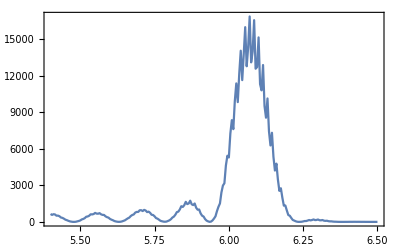

```mathematica
ListLinePlot[tk02sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
ll3ts1=AmplTwistTab[1,5.7/mee,5.7/mee (6/7)];
ll3tsm1=AmplTwistTab[-1,5.7/mee,5.7/mee (6/7)];
```

```mathematica
tm3s1=Table[{m,dProbabTwist[m,ll3ts1[[3]]]},{m,-mMax,mMax}];
tm3sm1=Table[{m,dProbabTwist[m,ll3tsm1[[3]]]},{m,-mMax,mMax}];
```

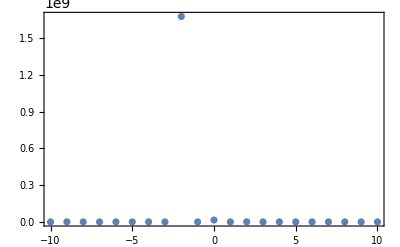
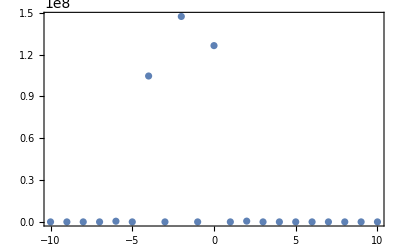

```mathematica
{ListPlot[tm3s1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tm3sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
ll4ts1=AmplTwistTab[1,6.08/mee,6.08/mee (6/7)];
ll4tsm1=AmplTwistTab[-1,6.08/mee,6.08/mee (6/7)];
```

```mathematica
tm4s1=Table[{m,dProbabTwist[m,ll4ts1[[3]]]},{m,-mMax,mMax}];
tm4sm1=Table[{m,dProbabTwist[m,ll4tsm1[[3]]]},{m,-mMax,mMax}];
```

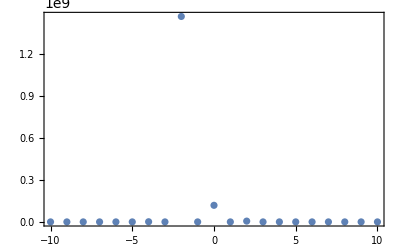
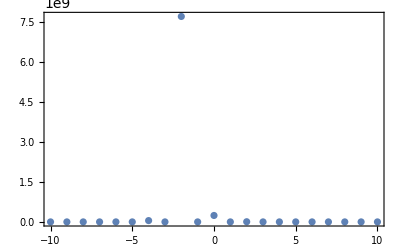

```mathematica
{ListPlot[tm4s1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tm4sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*нужно ещё расмотреть излучение от тяжелых ядер с малым гамма*)
```

```mathematica
(*старое*)
```